```mathematica
Clear["Global`*"]
```

```mathematica
SDtest[omega0_,etac_,Gamma_]:=Module[{ω0=omega0,ηc=etac,Γ=Gamma},
(*Γ=ω0^2/wc;*)
(*coupling strength and cut-off frequency in reaction coordinate*)
Λ=100000;
(*Mode frequency and spin-mode coupling*)
ω=ω0 //N;
κ=Sqrt[(π ηc ω0)/2];
γ=N[Γ/(2π ω0)];
Jrc[w_]:=γ w ;
(*check convergence*)
Jsb[v_]:=(ηc Γ ω0^2 v)/((ω0^2-v^2)^2+Γ^2 v^2);
J[v_,γ_,Λ_]:=γ v Exp[-v/Λ];
f[x_]:=ExpIntegralEi[x]-Exp[2x]ExpIntegralEi[-x];
Jcon[v_,γ_,Λ_]:=(4 κ^2 ω^2 J[v,γ,Λ])/((v^2-ω^2-2ω J[v,γ,Λ]f[v/Λ])^2+4 π^2 ω^2(J[v,γ,Λ])^2);
{concheck=Plot[{Jcon[v,γ,Λ],Jsb[v]},{v,0,400},PlotRange->{0,All},Frame->True],Integrate[Jsb[v]/v,{v,0,∞}]}]
```

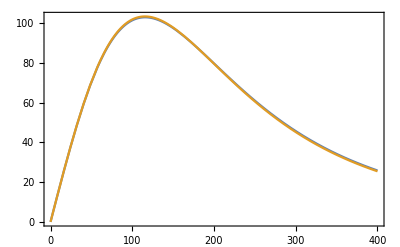
{-Graphics-,250.+0. ⅈ}

```mathematica
SDtest[200.0,N[500/π],200.0^2/100.0]
```

```mathematica
SteadySol[epsilon_,bias_,foerster_,phononbeta_,photonbeta_,omega0_,etac_,Gamma_,gammaEM_,statesnum_]:=Module[{ϵ=epsilon,ϵb=bias,V=foerster,β=phononbeta,βphoton=photonbeta,ω0=omega0,ηc=etac,Γ=Gamma,ΓEM=gammaEM,nstates=statesnum},
st=AbsoluteTime[];
Off[Eigensystem::arh];
Jsb[v_]:=(ηc Γ ω0^2 v)/((ω0^2-v^2)^2+Γ^2 v^2);
SBReorg=Integrate[Jsb[v]/v,{v,0,∞}];
ϵ1=ϵ+ϵb+SBReorg;ϵ2=ϵ+SBReorg;
(*Γ=ω0^2/wc;*)
ω=ω0 //N;
κ=Sqrt[(π ηc ω0)/2];
γ=N[Γ/(2π ω0)];
Jrc[w_]:=γ w ;

tensor[a___]:=KroneckerProduct[a];qeye[n_]:=Array[KroneckerDelta[#1,#2]&,{n,n}];dag[a_]:=ConjugateTranspose[a];

sx={{0,1},{1,0}};
sy={{0,-ⅈ},{ⅈ,0}};
sz={{1,0},{0,-1}};
sp=(sx+ⅈ sy)/2;
sm=(sx-ⅈ sy)/2;
c[a_,b_]:=a.b-b.a;
ac[a_,b_]:=a.b+b.a;
kp[a_,b_,c_,d_]:=KroneckerProduct[a,b,c,d];
out[a_,b_]:=Outer[Times,a,b];
id[n_]:=DiagonalMatrix[Table[1,{ii,1,n}]];
a[n_]:=Table[ Sqrt[i]*KroneckerDelta[i+1,j],{i,1,n},{j,1,n}]//N;
ad[n_]:=Table[ Sqrt[(i-1)]*KroneckerDelta[i,j+1],{i,1,n},{j,1,n}]//N;
zeromat[n_]:=ConstantArray[0,{4 n^2,4 n^2}];
occupation[ω_]:=1/(Exp[β ω]-1);
occupationphoton[ω_]:=1/(Exp[βphoton ω]-1);
(*define density operator*)
dens[n_]:=Array[Subscript[ρ, ##][t]&,{4 n^2,4 n^2}];
(*Hamiltonian*)
H[n_]:=SparseArray[ϵ1 KroneckerProduct[(id[2]+sz)/2,id[2],id[n],id[n]]+ϵ2 KroneckerProduct[id[2],(id[2]+sz)/2,id[n],id[n]]+V(KroneckerProduct[sp,sm,id[n],id[n]]+KroneckerProduct[sm,sp,id[n],id[n]])-κ KroneckerProduct[(id[2]+sz)/2,id[2],a[n]+ad[n],id[n]]-κ KroneckerProduct[id[2],(id[2]+sz)/2,id[n],a[n]+ad[n]]+ω KroneckerProduct[id[2],id[2],ad[n].a[n],id[n]]+ω KroneckerProduct[id[2],id[2],id[n],ad[n].a[n]]//N];
(*define intial conditions*)
initialmode[n_]:=(1/Tr[MatrixExp[-β ω ad[n].a[n]]]*MatrixExp[-β ω ad[n].a[n]]);
initialspin[n_]:=KroneckerProduct[{{0,0},{0,1}},{{0,0},{0,1}}];
initialdens[n_]:=KroneckerProduct[initialspin[n],initialmode[n],initialmode[n]]//Flatten;
initialddens[n_]:=KroneckerProduct[initialspin[n],initialmode[n],initialmode[n]];
initialcond[n_]:=Thread[Flatten[dens[n]/.t->0]==Flatten[KroneckerProduct[initialspin[n],initialmode[n],initialmode[n]]]];

n=nstates;
{vals,vecs}=Eigensystem[H[n]];
nvecs=ParallelMap[Normalize[#1]&,vecs]//Chop;
dHam=DiagonalMatrix[vals];
λ=Chop[ParallelTable[vals⟦i⟧-vals⟦j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],10^-7];
Φ[i_,j_]:=out[nvecs⟦i⟧,Conjugate[nvecs⟦j⟧]];
ph=Sum[Φ[i,j],{i,1,n},{j,1,n}];

qid=SparseArray[qeye[4 n^2]];
(*Pre multiplying super operator*)
spre[A_]:=SparseArray[tensor[A,qid]];
(*post multiplying super operator*)
spost[A_]:=SparseArray[tensor[qid,Transpose[A]]];
(*pre and post multiplication*)
sprepost[A_,B_]:=SparseArray[tensor[A,Transpose[B]]];
VecLind[A_]:=2*sprepost[A,dag[A]]-spre[dag[A].A]-spost[dag[A].A];

(*overlap between position and eigenstates*)
X1=SparseArray[Chop[ParallelTable[nvecs⟦i⟧.kp[id[2],id[2],a[n]+ad[n],id[n]].nvecs⟦j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],10^-7]];
X2=SparseArray[Chop[ParallelTable[nvecs⟦i⟧.kp[id[2],id[2],id[n],a[n]+ad[n]].nvecs⟦j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],10^-7]];
χ1=SparseArray[Chop[ParallelTable[π/2 γ If[λ⟦i,j⟧==0,2/β,λ⟦i,j⟧Coth[(β λ⟦i,j⟧)/2]]X1⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],10^-7]];
χ2=SparseArray[Chop[ParallelTable[π/2 γ If[λ⟦i,j⟧==0,2/β,λ⟦i,j⟧Coth[(β λ⟦i,j⟧)/2]]X2⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],10^-7]];
Ξ1=SparseArray[Chop[ParallelTable[π/2 Jrc[λ⟦i,j⟧]nvecs⟦i⟧.kp[id[2],id[2],a[n]+ad[n],id[n]].nvecs⟦j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],10^-7]];
Ξ2=SparseArray[Chop[ParallelTable[π/2 Jrc[λ⟦i,j⟧]nvecs⟦i⟧.kp[id[2],id[2],id[n],a[n]+ad[n]].nvecs⟦j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],10^-7]];

αEM=ΓEM/(2π ϵ1);
Jem[ω_]:=αEM ω;
A1=Chop[SparseArray[(kp[sp,id[2],id[n],id[n]]+kp[id[2],sp,id[n],id[n]])],10^-7];
A2=Chop[SparseArray[(kp[sm,id[2],id[n],id[n]]+kp[id[2],sm,id[n],id[n]])],10^-7];
A1eig=Chop[SparseArray[Chop[nvecs.A1.ConjugateTranspose[nvecs]]],10^-7];
A2eig=Chop[SparseArray[Chop[nvecs.A2.ConjugateTranspose[nvecs]]],10^-7];
A1abs=Chop[SparseArray[Chop[ConjugateTranspose[nvecs].ParallelTable[π If[λ⟦i,j⟧==0,1/2 αEM/βphoton,HeavisideTheta[λ⟦i,j⟧] Jem[λ⟦i,j⟧] occupationphoton[λ⟦i,j⟧]]A1eig⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}].nvecs]],10^-7];
A1emit=Chop[SparseArray[Chop[ConjugateTranspose[nvecs].ParallelTable[π If[λ⟦i,j⟧==0,1/2 αEM/βphoton,HeavisideTheta[λ⟦i,j⟧] Jem[λ⟦i,j⟧] (1+occupationphoton[λ⟦i,j⟧])]A1eig⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}].nvecs]],10^-7];
A2abs=Chop[SparseArray[Chop[ConjugateTranspose[nvecs].ParallelTable[π If[λ⟦i,j⟧==0,1/2 αEM/βphoton,HeavisideTheta[-λ⟦i,j⟧] Jem[-λ⟦i,j⟧] occupationphoton[-λ⟦i,j⟧]]A2eig⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}].nvecs]],10^-7];
A2emit=Chop[SparseArray[Chop[ConjugateTranspose[nvecs].ParallelTable[π If[λ⟦i,j⟧==0,1/2 αEM/βphoton,HeavisideTheta[-λ⟦i,j⟧] Jem[-λ⟦i,j⟧](1+ occupationphoton[-λ⟦i,j⟧])]A2eig⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}].nvecs]],10^-7];

(*st=AbsoluteTime[];*)ℒphoton=Chop[SparseArray[-spre[A1.A2emit]+sprepost[A2emit,A1]-spost[A2abs.A1]+sprepost[A1,A2abs]-spre[A2.A1abs]+sprepost[A1abs,A2]-spost[A1emit.A2]+sprepost[A2,A1emit]],10^-7];
(*en=AbsoluteTime[];
Print[en-st];*)

iX1=Chop[SparseArray[Inverse[vecs].X1.vecs],10^-7];
iχ1=Chop[SparseArray[Inverse[vecs].χ1.vecs],10^-7];
iΞ1=Chop[SparseArray[Inverse[vecs].Ξ1.vecs],10^-7];
iX2=Chop[SparseArray[Inverse[vecs].X2.vecs],10^-7];
iχ2=Chop[SparseArray[Inverse[vecs].χ2.vecs],10^-7];
iΞ2=Chop[SparseArray[Inverse[vecs].Ξ2.vecs],10^-7];

(*st=AbsoluteTime[];*)
Louv=SparseArray[With[{Ham=H[n]},Chop[-ⅈ(spre[Ham]-spost[Ham])-(spre[iX1.iχ1]-sprepost[iX1,iχ1]-sprepost[iχ1,iX1]+spost[iχ1.iX1])+(spre[iX1.iΞ1]+sprepost[iX1,iΞ1]-sprepost[iΞ1,iX1]-spost[iΞ1.iX1])-(spre[iX2.iχ2]-sprepost[iX2,iχ2]-sprepost[iχ2,iX2]+spost[iχ2.iX2])+(spre[iX2.iΞ2]+sprepost[iX2,iΞ2]-sprepost[iΞ2,iX2]-spost[iΞ2.iX2])+ℒphoton,10^-7]]];
(*en=AbsoluteTime[];
Print["Liouvillian took ", en-st," seconds to build"];*)

(*Print["Liouvillian: ",Louv];*)

(*st=AbsoluteTime[];*)
dsolss=With[{runorm=Partition[Eigenvectors[Louv,-1(*,Method->{"Arnoldi","Tolerance"->10^-8,"MaxIterations"->6000,"Shift"->10^-15}*)]⟦1⟧,4 n^2]},Chop[runorm/Tr[runorm],10^-7]];
(*en=AbsoluteTime[];
Print["Steady-state solution took ", en-st," seconds"];*)

sz1expecss=Chop[Tr[kp[sz,id[2],id[n],id[n]].(dsolss)]];
sx1expecss=Chop[Tr[kp[sx,id[2],id[n],id[n]].(dsolss)]];
numb1ss=Chop[Tr[kp[id[2],id[2],ad[n].a[n],id[n]].(dsolss)]];
sz2expecss=Chop[Tr[kp[id[2],sz,id[n],id[n]].(dsolss)]];
sx2expecss=Chop[Tr[kp[id[2],sx,id[n],id[n]].(dsolss)]];
numb2ss=Chop[Tr[kp[id[2],id[2],id[n],ad[n].a[n]].(dsolss)]];
sp1sm2expecss=Chop[Tr[kp[sp,sm,id[n],id[n]].(dsolss)]];
sm1sp2expecss=Chop[Tr[kp[sm,sp,id[n],id[n]].(dsolss)]];
HDimer=ϵ1 KroneckerProduct[(id[2]+sz)/2,id[2]]+ϵ2 KroneckerProduct[id[2],(id[2]+sz)/2]+V(KroneckerProduct[sp,sm]+KroneckerProduct[sm,sp]);
doublepop=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦1⟧,Eigenvectors[HDimer]⟦1⟧],id[n],id[n]].dsolss]];
e2pop=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦2⟧,Eigenvectors[HDimer]⟦2⟧],id[n],id[n]].dsolss]];
e1pop=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦3⟧,Eigenvectors[HDimer]⟦3⟧],id[n],id[n]].dsolss]];
e0pop=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦4⟧,Eigenvectors[HDimer]⟦4⟧],id[n],id[n]].dsolss]];
e21coh=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦2⟧,Eigenvectors[HDimer]⟦3⟧],id[n],id[n]].dsolss]];
e12coh=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦3⟧,Eigenvectors[HDimer]⟦2⟧],id[n],id[n]].dsolss]];
(*Export[TextString[Row[{Directory[],"/Data/RC_EM_Dimer/","ssn",nstates,".dat"}]],dsolss];*)
{e0pop,e1pop,e2pop,doublepop,Abs[e12coh](*,e21coh*)}]
```

```mathematica
(*SteadySol[epsilon_,bias_,foerster_,phononbeta_,photonbeta_,omega0_,etac_,Gamma_,gammaEM_,statesnum_]*)
```

```mathematica
SteadySol[1.4 8065.5,0.0 8065.5,0.001 8065.5,1/(0.695 300),1/(0.695 6000),200.0,N[0.01/π],200.0^2/100.0,5.309 10^-3,4]
```

{0.874965,0.0629141,0.0582304,0.00389035,0}

```mathematica
alphatable4states=Table[{α,SteadySol[1.4 8065.5,0.0 8065.5,0.001 8065.5,1/(0.695 300),1/(0.695 6000),200.0,N[α/π],200.0^2/100.0,5.309 10^-3,4]},{α,0.01,1000,10}];
```

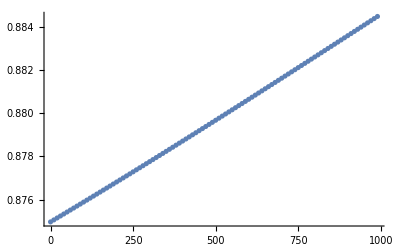

```mathematica
ListPlot[Transpose[Join[{alphatable4states⟦All,1⟧},{alphatable4states⟦All,2,1⟧}]]]
```

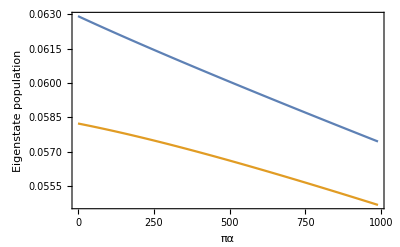

```mathematica
ListPlot[{Transpose[Join[{alphatable4states⟦All,1⟧},{alphatable4states⟦All,2,2⟧}]],Transpose[Join[{alphatable4states⟦All,1⟧},{alphatable4states⟦All,2,3⟧}]]},Joined->True,Frame->True,FrameLabel->{"πα","Eigenstate population"}]
```

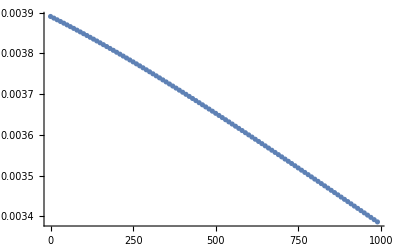

```mathematica
ListPlot[Transpose[Join[{alphatable4states⟦All,1⟧},{alphatable4states⟦All,2,4⟧}]]]
```

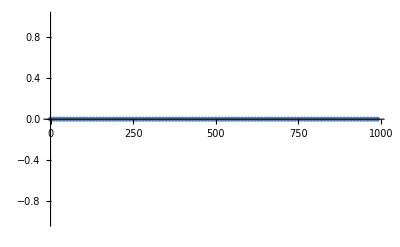

```mathematica
ListPlot[Transpose[Join[{alphatable4states⟦All,1⟧},{alphatable4states⟦All,2,5⟧}]]]
```

```mathematica
convergencetab=Table[{num,SteadySol[1.4 8065.5,0.0 8065.5,0.001 8065.5,1/(0.695 300),1/(0.695 6000),200.0,N[500.0/π],200.0^2/100.0,5.309 10^-3,num]},{num,2,8,1}]
```

{{2,{0.8807,0.0598308,0.0559086,0.00356034,0}},{3,{0.880102,0.0599544,0.056328,0.00361508,0}},{4,{0.879678,0.0600544,0.0566143,0.00365293,0}},{5,{0.879379,0.0601301,0.0568117,0.00367925,0}},{6,{0.879171,0.0601856,0.0569463,0.0036973,0}},{7,{0.879029,0.0602248,0.0570364,0.00370941,0}},{8,{0.878936,0.0602517,0.0570949,0.0037173,0}}}

```mathematica
(* Command Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,i⟧}]] puts data in more convenient form i.e. pairs of points (n,value) for whichever observable is chosen through i *)
Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,1⟧}]]
```

{{2,0.8807},{3,0.880102},{4,0.879678},{5,0.879379},{6,0.879171},{7,0.879029},{8,0.878936}}

```mathematica
(* Fitted values *)
e0popfit=cc/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,1⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7]
e1popfit=cc/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,2⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7]
e2popfit=cc/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,3⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7]
doublepopfit=cc/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,4⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7]
Abse12cohfit=cc/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,5⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7]
```

0.878698

0.0603466

0.0572296

0.00373615

0.

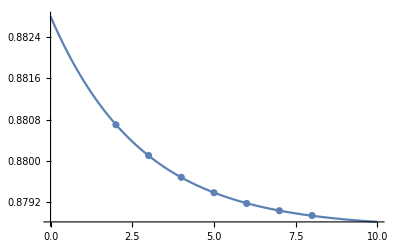

```mathematica
Show[Plot[(aa Exp[-bb xx]+cc)/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,1⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7],{xx,0,10}],ListPlot[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,1⟧}]]]]
```

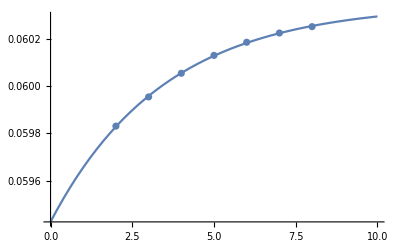

```mathematica
Show[Plot[(aa Exp[-bb xx]+cc)/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,2⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7],{xx,0,10}],ListPlot[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,2⟧}]]]]
```

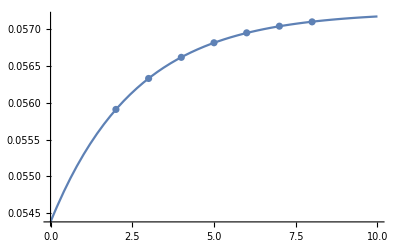

```mathematica
Show[Plot[(aa Exp[-bb xx]+cc)/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,3⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7],{xx,0,10}],ListPlot[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,3⟧}]]]]
```

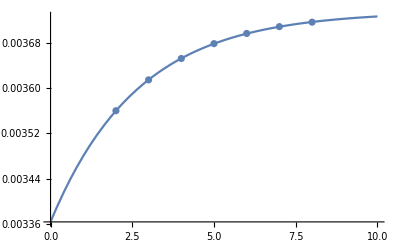

```mathematica
Show[Plot[(aa Exp[-bb xx]+cc)/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,4⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7],{xx,0,10}],ListPlot[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,4⟧}]]]]
```

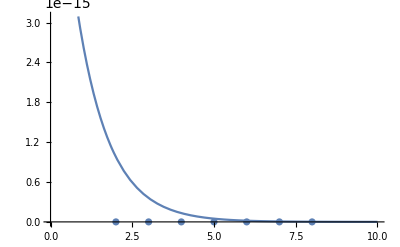

```mathematica
Show[Plot[(aa Exp[-bb xx]+cc)/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,5⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7],{xx,0,10}],ListPlot[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,5⟧}]]]]
```